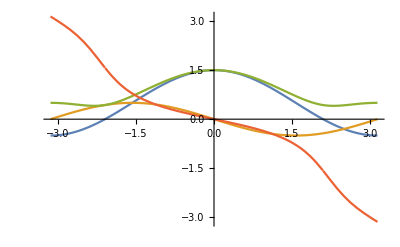

```mathematica
nn=501;
ll=IntegerPart[nn/10];
prec=528;
nData=10;
γ=0.5//N[#,prec]&;
λ=0.5//N[#,prec]&;
a0=λ//N[#,prec]&;
a1=(1-γ)/2//N[#,prec]&;
a2=(1+γ)/2//N[#,prec]&;
α[θ_]=(a0+(a2+a1) Cos[θ]);
β[θ_]=(a1-a2) Sin[θ];
ω[θ_]=Sqrt[α[θ]^2+β[θ]^2];
ϕ[θ_]=ArcTan[α[θ],β[θ]];
Plot[{α[x],β[x],ω[x],ϕ[x]},{x,-π,π}]
```

```mathematica
t=Table[k,{k,-(nn-1)/2,(nn-1)/2}];
μ=0//N[#,prec]&;
βT=RandomReal[{1/1000,1/1100}]//N[#,prec]&;
p[l_]=1/(Exp[βT (ω[((2 π)/nn) l]-μ)]+1);
mCos=Table[If[RandomReal[]>p[k],-(1/2),1/2],{k,1,(nn-1)/2}];
mCos0=If[RandomReal[]>p[0],-(1/2),1/2];
mSin=Table[If[RandomReal[]>p[k],-(1/2),1/2],{k,1,(nn-1)/2}];
mSin0=If[RandomReal[]>p[0],-(1/2),1/2];
MPlusBand=((If[#==0,(mCos0+mSin0)/2,(mCos⟦Abs[#]⟧+mSin⟦Abs[#]⟧)/2]) E^(I Sign[(2 π)/nn #] ϕ[Abs[(2 π)/nn #]])&/@t)//RotateLeft[#,(nn-1)/2]&//Fourier;
MMinusAntiBand=((If[#==0,(mCos0-mSin0)/2,(mCos⟦Abs[#]⟧-mSin⟦Abs[#]⟧)/2]) E^(I Sign[(2 π)/nn #] ϕ[Abs[(2 π)/nn #]])&/@t)//RotateLeft[#,(nn-1)/2]&//Fourier;
Resultado=Join[Take[MPlusBand,ll],Take[MMinusAntiBand,ll]];
```

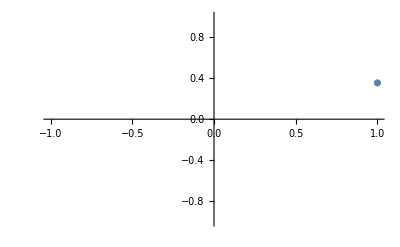

```mathematica
Resultado//ListPlot
```

```mathematica
t=Table[k,{k,-(nn-1)/2,(nn-1)/2}];
μ=0//N[#,prec]&;
βT=1/1000//N[#,prec]&;
mCos=Table[0.5,{k,1,(nn-1)/2}];
mCos0=1/2;
mSin=Table[1/2,{k,1,(nn-1)/2}];
mSin0=1/2;
MPlusBand=((If[#==0,(mCos0+mSin0)/2,(mCos⟦Abs[#]⟧+mSin⟦Abs[#]⟧)/2]) E^(I Sign[(2 π)/nn #] ϕ[Abs[(2 π)/nn #]])&/@t)//RotateLeft[#,(nn-1)/2]&//Fourier;
MMinusAntiBand=((If[#==0,(mCos0-mSin0)/2,(mCos⟦Abs[#]⟧-mSin⟦Abs[#]⟧)/2]) E^(I Sign[(2 π)/nn #] ϕ[Abs[(2 π)/nn #]])&/@t)//RotateLeft[#,(nn-1)/2]&//Fourier;
```

```mathematica
Real[MPlusBand]
```

Real[{3.32004-3.53408×10^-17 ⅈ,9.91422+4.85809×10^-16 ⅈ,-3.61969+1.6418×10^-16 ⅈ,0.220416+1.44332×10^-16 ⅈ,0.671613-1.73787×10^-16 ⅈ,-0.4473-4.63754×10^-17 ⅈ,0.0904994+1.96462×10^-16 ⅈ,0.0684518-7.80963×10^-17 ⅈ,-0.0681799-8.28092×10^-17 ⅈ,0.0227041+1.21941×10^-16 ⅈ,0.00586778+1.59034×10^-16 ⅈ,-0.0105183-2.22305×10^-16 ⅈ,0.00491838+1.82883×10^-17 ⅈ,0.0000680478+2.17811×10^-17 ⅈ,-0.00155565+3.30099×10^-16 ⅈ,0.000979076-1.19863×10^-17 ⅈ,-0.000147339-3.34893×10^-17 ⅈ,-0.00021062+2.32486×10^-17 ⅈ,0.000182488-2.38429×10^-16 ⅈ,-0.0000520081-1.52163×10^-16 ⅈ,-0.0000238428+4.4363×10^-17 ⅈ,0.0000319611+1.09895×10^-16 ⅈ,-0.000013234-3.68955×10^-17 ⅈ,-1.54387×10^-6-1.84358×10^-16 ⅈ,5.22519×10^-6+7.13669×10^-17 ⅈ,-2.91788×10^-6-5.15367×10^-17 ⅈ,2.34733×10^-7-4.96973×10^-17 ⅈ,7.81521×10^-7+1.42022×10^-17 ⅈ,-5.86701×10^-7+4.77784×10^-18 ⅈ,1.33×10^-7+9.61518×10^-17 ⅈ,1.01649×10^-7+7.49826×10^-17 ⅈ,-1.09485×10^-7+1.59472×10^-18 ⅈ,3.90287×10^-8+3.54873×10^-17 ⅈ,9.73642×10^-9-3.03191×10^-17 ⅈ,-1.90061×10^-8+1.71868×10^-16 ⅈ,9.33489×10^-9-1.38793×10^-16 ⅈ,1.91798×10^-11-2.18694×10^-17 ⅈ,-3.03743×10^-9-2.17003×10^-17 ⅈ,1.99138×10^-9+7.16564×10^-17 ⅈ,-3.24398×10^-10+1.05808×10^-16 ⅈ,-4.33211×10^-10+1.2275×10^-16 ⅈ,3.90617×10^-10+2.13282×10^-16 ⅈ,-1.16368×10^-10+1.71318×10^-16 ⅈ,-5.04385×10^-11+3.97409×10^-17 ⅈ,7.11189×10^-11+1.51446×10^-17 ⅈ,-3.04446×10^-11-7.67446×10^-17 ⅈ,-3.10679×10^-12+1.08504×10^-16 ⅈ,1.19754×10^-11+2.87051×10^-16 ⅈ,-6.88527×10^-12+1.41476×10^-16 ⅈ,6.33953×10^-13+2.41654×10^-16 ⅈ,1.82968×10^-12-7.8881×10^-18 ⅈ,-1.41472×10^-12-1.01661×10^-16 ⅈ,3.36118×10^-13-1.40003×10^-16 ⅈ,2.40551×10^-13+1.14062×10^-16 ⅈ,-2.68844×10^-13-1.08085×10^-16 ⅈ,9.87153×10^-14+3.16249×10^-17 ⅈ,2.29063×10^-14-6.27227×10^-17 ⅈ,-4.77282×10^-14-1.17842×10^-17 ⅈ,2.38986×10^-14-4.72903×10^-17 ⅈ,-1.46854×10^-16+3.71068×10^-17 ⅈ,-7.58244×10^-15-9.02964×10^-17 ⅈ,5.27792×10^-15-1.05436×10^-16 ⅈ,-9.7125×10^-16+9.89085×10^-17 ⅈ,-1.01583×10^-15+1.78362×10^-16 ⅈ,9.73026×10^-16-1.83996×10^-16 ⅈ,-5.76465×10^-16-9.12119×10^-17 ⅈ,-3.08723×10^-17+9.20583×10^-17 ⅈ,1.28997×10^-16+1.16876×10^-16 ⅈ,4.67192×10^-19+1.01953×10^-16 ⅈ,-2.12859×10^-16+1.78094×10^-16 ⅈ,1.33689×10^-16-1.19187×10^-16 ⅈ,6.81222×10^-17-9.05053×10^-17 ⅈ,-1.80195×10^-16+4.81323×10^-17 ⅈ,4.37907×10^-16+1.59488×10^-16 ⅈ,9.16931×10^-17+4.45932×10^-17 ⅈ,9.2192×10^-17-1.85112×10^-16 ⅈ,9.79133×10^-17+2.74972×10^-16 ⅈ,-9.95802×10^-17-6.56528×10^-17 ⅈ,2.98095×10^-18+1.65307×10^-16 ⅈ,6.92365×10^-17-6.06861×10^-17 ⅈ,-3.7931×10^-17-4.72078×10^-17 ⅈ,-4.5588×10^-17+2.5468×10^-16 ⅈ,2.36622×10^-16+1.36582×10^-16 ⅈ,4.07527×10^-17-1.2778×10^-17 ⅈ,-7.6306×10^-17+1.36162×10^-16 ⅈ,-6.22496×10^-17-1.6859×10^-16 ⅈ,-1.555×10^-16-1.27722×10^-16 ⅈ,6.18628×10^-17+6.36675×10^-17 ⅈ,-3.1835×10^-16+2.52771×10^-16 ⅈ,8.23163×10^-17+1.83471×10^-17 ⅈ,-1.27567×10^-16+7.84887×10^-17 ⅈ,-3.35966×10^-17-1.09002×10^-16 ⅈ,-4.48641×10^-17-2.20437×10^-17 ⅈ,-3.99621×10^-17-9.39679×10^-17 ⅈ,-2.56035×10^-18+1.07559×10^-16 ⅈ,-1.27288×10^-16+4.09657×10^-17 ⅈ,2.28403×10^-16-8.93715×10^-17 ⅈ,9.93008×10^-17+2.61559×10^-16 ⅈ,-2.39852×10^-16+5.22394×10^-17 ⅈ,4.92094×10^-17+1.87432×10^-16 ⅈ,3.84139×10^-17-1.46076×10^-16 ⅈ,-2.28857×10^-16-9.01578×10^-17 ⅈ,1.61519×10^-16+2.28259×10^-16 ⅈ,2.99×10^-17+2.96466×10^-17 ⅈ,-1.78879×10^-17-1.18707×10^-16 ⅈ,7.14295×10^-17+1.05007×10^-16 ⅈ,9.32839×10^-17-6.91623×10^-18 ⅈ,-2.60397×10^-17-6.43385×10^-17 ⅈ,9.52739×10^-17+1.1333×10^-18 ⅈ,-1.93859×10^-17-2.68619×10^-16 ⅈ,-3.00614×10^-16-4.4366×10^-17 ⅈ,-1.16659×10^-16+4.69897×10^-17 ⅈ,1.6478×10^-16-7.62376×10^-17 ⅈ,-2.23707×10^-16-1.44399×10^-16 ⅈ,3.91005×10^-18+2.31429×10^-16 ⅈ,-2.08297×10^-16+6.36701×10^-17 ⅈ,1.50779×10^-16-7.9876×10^-17 ⅈ,-6.55967×10^-20-5.40231×10^-17 ⅈ,-3.72036×10^-17-1.71948×10^-16 ⅈ,-6.31862×10^-18-1.02842×10^-16 ⅈ,1.49748×10^-16+2.85186×10^-17 ⅈ,1.35327×10^-16-6.65986×10^-17 ⅈ,-1.18171×10^-16-9.37245×10^-17 ⅈ,1.00642×10^-16+4.69382×10^-17 ⅈ,4.75738×10^-17+1.68704×10^-16 ⅈ,6.06531×10^-17-3.42215×10^-17 ⅈ,-8.91613×10^-17-1.31316×10^-16 ⅈ,-8.73817×10^-17-3.43495×10^-17 ⅈ,-8.20645×10^-17-2.50821×10^-16 ⅈ,-2.46808×10^-16-3.38573×10^-17 ⅈ,-6.88341×10^-17-2.49664×10^-16 ⅈ,5.67128×10^-17-1.05849×10^-16 ⅈ,-1.39355×10^-17-2.78028×10^-17 ⅈ,-7.60291×10^-17-7.9727×10^-17 ⅈ,4.64597×10^-17+1.68323×10^-16 ⅈ,3.13545×10^-17+1.50711×10^-17 ⅈ,1.11295×10^-16+9.84984×10^-17 ⅈ,4.52755×10^-17-6.71323×10^-17 ⅈ,-1.63754×10^-16+1.20036×10^-18 ⅈ,1.84337×10^-16-5.77225×10^-17 ⅈ,1.64837×10^-16+9.74185×10^-17 ⅈ,-1.35567×10^-17+1.54931×10^-16 ⅈ,1.54195×10^-16-1.50926×10^-16 ⅈ,-2.07641×10^-16-2.19424×10^-17 ⅈ,-2.12232×10^-16-3.125×10^-18 ⅈ,2.06215×10^-17+1.80231×10^-16 ⅈ,-1.03685×10^-16-1.97106×10^-17 ⅈ,9.74548×10^-17+1.7254×10^-16 ⅈ,1.07093×10^-16+4.16351×10^-17 ⅈ,1.54545×10^-16+1.74106×10^-16 ⅈ,-1.64693×10^-16-3.75797×10^-17 ⅈ,5.03777×10^-17-3.02003×10^-16 ⅈ,5.68351×10^-17+2.91298×10^-18 ⅈ,-1.57676×10^-16+1.39985×10^-16 ⅈ,-1.5306×10^-16+2.07038×10^-16 ⅈ,-4.361×10^-18-4.76223×10^-17 ⅈ,7.90628×10^-17-7.44894×10^-17 ⅈ,-1.01879×10^-16-6.0553×10^-17 ⅈ,9.19268×10^-17+4.92327×10^-17 ⅈ,4.50447×10^-17+1.01111×10^-16 ⅈ,-2.28088×10^-16+2.77367×10^-18 ⅈ,9.45827×10^-17-1.53205×10^-16 ⅈ,1.27413×10^-16+3.83279×10^-17 ⅈ,-1.18833×10^-16-1.67021×10^-17 ⅈ,-1.67842×10^-16+6.51276×10^-17 ⅈ,-4.13942×10^-17-6.20662×10^-17 ⅈ,8.05385×10^-18-2.97663×10^-16 ⅈ,7.45964×10^-18+1.72606×10^-17 ⅈ,1.17556×10^-16-5.86603×10^-17 ⅈ,2.1998×10^-16+6.64254×10^-17 ⅈ,1.06845×10^-17-2.44201×10^-17 ⅈ,-1.87982×10^-16+1.00281×10^-16 ⅈ,1.71088×10^-16-2.95535×10^-17 ⅈ,-1.88314×10^-16+1.12534×10^-16 ⅈ,1.944×10^-18+2.56891×10^-16 ⅈ,-1.03748×10^-16-6.03713×10^-17 ⅈ,5.04566×10^-17-1.37438×10^-16 ⅈ,4.86417×10^-18-1.81276×10^-16 ⅈ,5.73784×10^-17+1.34417×10^-16 ⅈ,5.39783×10^-17+2.40904×10^-16 ⅈ,-2.47489×10^-16-6.2094×10^-17 ⅈ,8.66867×10^-17+4.8603×10^-17 ⅈ,-3.79856×10^-17-3.15919×10^-16 ⅈ,5.56809×10^-17+4.08738×10^-17 ⅈ,1.74504×10^-16+6.55836×10^-17 ⅈ,-6.8002×10^-18+4.60971×10^-17 ⅈ,1.0963×10^-16-1.09318×10^-16 ⅈ,-6.14061×10^-17-1.43188×10^-17 ⅈ,5.0424×10^-17+1.85572×10^-16 ⅈ,-1.18135×10^-16+1.80895×10^-16 ⅈ,2.18654×10^-18-4.44665×10^-17 ⅈ,-7.85027×10^-17-1.00463×10^-16 ⅈ,-2.26343×10^-16+1.1512×10^-16 ⅈ,-8.29182×10^-17-5.94216×10^-16 ⅈ,1.5878×10^-16+6.243×10^-17 ⅈ,-1.47146×10^-17+9.57088×10^-17 ⅈ,1.57611×10^-16-3.35371×10^-17 ⅈ,1.93022×10^-16-1.67267×10^-16 ⅈ,1.37525×10^-16-2.95826×10^-17 ⅈ,1.59794×10^-16+2.58245×10^-16 ⅈ,2.10287×10^-18+3.22675×10^-17 ⅈ,7.51652×10^-17+2.54729×10^-17 ⅈ,-5.83263×10^-17+2.26476×10^-16 ⅈ,-3.46635×10^-17-2.0218×10^-16 ⅈ,-1.06578×10^-18-3.52539×10^-17 ⅈ,-1.18227×10^-18+4.0772×10^-17 ⅈ,-3.75323×10^-16+1.87958×10^-16 ⅈ,-3.6195×10^-17+3.5428×10^-17 ⅈ,2.67541×10^-16+2.58687×10^-17 ⅈ,2.27028×10^-17+2.71873×10^-18 ⅈ,1.74111×10^-16+3.30093×10^-16 ⅈ,3.37523×10^-17-5.10637×10^-17 ⅈ,1.22907×10^-16-1.14794×10^-16 ⅈ,-1.67091×10^-16-1.4371×10^-16 ⅈ,7.14881×10^-17-4.10603×10^-17 ⅈ,1.33055×10^-16+1.02083×10^-17 ⅈ,6.58993×10^-17+4.20485×10^-17 ⅈ,3.5803×10^-16-1.02289×10^-16 ⅈ,1.18415×10^-16-7.53968×10^-17 ⅈ,1.54318×10^-16-1.53071×10^-16 ⅈ,-9.56705×10^-17+1.56277×10^-17 ⅈ,1.55076×10^-16-2.90459×10^-17 ⅈ,1.17785×10^-16-4.19783×10^-17 ⅈ,-2.52117×10^-16+4.69866×10^-17 ⅈ,-8.42968×10^-17+1.71907×10^-16 ⅈ,-2.18321×10^-16-9.9839×10^-17 ⅈ,-9.50471×10^-17+7.35902×10^-17 ⅈ,-1.23127×10^-16+4.09904×10^-17 ⅈ,1.27858×10^-17+9.52054×10^-17 ⅈ,-5.89834×10^-17-5.13205×10^-17 ⅈ,-2.92411×10^-16-5.03707×10^-17 ⅈ,1.78953×10^-16+9.91528×10^-17 ⅈ,8.30621×10^-17+2.58611×10^-16 ⅈ,8.26212×10^-17-1.0105×10^-16 ⅈ,5.89015×10^-17-6.7382×10^-17 ⅈ,-5.40094×10^-17+1.01961×10^-16 ⅈ,5.42634×10^-17+5.29316×10^-17 ⅈ,5.50632×10^-17-1.56005×10^-17 ⅈ,-4.41078×10^-17+3.5371×10^-16 ⅈ,2.78909×10^-17+9.80728×10^-17 ⅈ,-1.40622×10^-16-8.05248×10^-17 ⅈ,2.77781×10^-16+2.86843×10^-16 ⅈ,6.40325×10^-17+1.3754×10^-16 ⅈ,2.66889×10^-17-5.18707×10^-17 ⅈ,2.62583×10^-16-2.67241×10^-17 ⅈ,-4.9364×10^-16-3.20078×10^-17 ⅈ,-2.43334×10^-16-9.88747×10^-17 ⅈ,4.83678×10^-18-1.19974×10^-16 ⅈ,1.59608×10^-17-2.4194×10^-16 ⅈ,3.15628×10^-16-4.45348×10^-18 ⅈ,1.91061×10^-17-1.17526×10^-16 ⅈ,-1.35213×10^-16-1.1553×10^-16 ⅈ,1.8326×10^-16+3.09597×10^-16 ⅈ,-4.17459×10^-17-1.24724×10^-16 ⅈ,-2.45066×10^-16-1.67576×10^-16 ⅈ,1.10831×10^-16-8.04456×10^-17 ⅈ,-3.70075×10^-17+1.60675×10^-16 ⅈ,-1.35989×10^-16+1.78162×10^-17 ⅈ,1.09484×10^-16-4.7778×10^-17 ⅈ,2.65048×10^-17-9.57967×10^-17 ⅈ,2.1608×10^-16-9.15553×10^-17 ⅈ,-3.98315×10^-17+2.61352×10^-17 ⅈ,-2.74384×10^-16+1.1135×10^-16 ⅈ,2.1482×10^-17+1.34792×10^-16 ⅈ,-2.27189×10^-17+1.66003×10^-16 ⅈ,2.30807×10^-17-4.38513×10^-17 ⅈ,-1.25929×10^-16-7.75182×10^-17 ⅈ,1.96215×10^-17+3.97896×10^-17 ⅈ,9.1198×10^-17+1.27277×10^-16 ⅈ,1.86643×10^-16+8.79746×10^-17 ⅈ,-6.20054×10^-17-4.32188×10^-17 ⅈ,-1.26443×10^-17-1.67937×10^-16 ⅈ,2.29491×10^-17+4.4082×10^-17 ⅈ,-1.56148×10^-16+8.69513×10^-17 ⅈ,-1.92857×10^-16+2.51591×10^-17 ⅈ,2.25712×10^-17+2.14209×10^-16 ⅈ,2.05573×10^-16+6.54002×10^-17 ⅈ,-1.8539×10^-16+1.59903×10^-16 ⅈ,-7.72896×10^-17+2.17661×10^-16 ⅈ,-2.33492×10^-17-1.50276×10^-16 ⅈ,1.82765×10^-16+2.23462×10^-17 ⅈ,8.44528×10^-17-1.043×10^-16 ⅈ,1.16775×10^-16-8.50913×10^-17 ⅈ,1.47919×10^-16-6.95622×10^-17 ⅈ,-4.68692×10^-17+3.07866×10^-17 ⅈ,-1.51676×10^-16-4.15493×10^-17 ⅈ,4.93334×10^-17-5.47191×10^-18 ⅈ,1.5345×10^-17-4.46053×10^-17 ⅈ,1.55779×10^-16-1.49109×10^-16 ⅈ,-8.72942×10^-18-9.88582×10^-17 ⅈ,2.99173×10^-16+9.09618×10^-17 ⅈ,2.4641×10^-16+6.84714×10^-17 ⅈ,1.01535×10^-17-1.14197×10^-16 ⅈ,-5.41642×10^-17+2.04538×10^-17 ⅈ,-1.47729×10^-16-2.50321×10^-17 ⅈ,-2.39891×10^-16-2.62398×10^-17 ⅈ,1.38905×10^-16+8.08037×10^-17 ⅈ,1.28766×10^-16-2.63992×10^-17 ⅈ,-1.76541×10^-16+1.37753×10^-17 ⅈ,2.15675×10^-17-8.20114×10^-18 ⅈ,-1.49913×10^-16+1.35438×10^-16 ⅈ,4.74194×10^-17-6.52138×10^-18 ⅈ,-1.22435×10^-17+2.36435×10^-16 ⅈ,-6.06739×10^-17-3.6542×10^-17 ⅈ,1.0699×10^-16-7.5071×10^-18 ⅈ,7.88895×10^-17+8.99407×10^-18 ⅈ,8.90504×10^-18+4.21368×10^-17 ⅈ,-2.45487×10^-16+1.04112×10^-16 ⅈ,4.9573×10^-17-2.19755×10^-17 ⅈ,1.56426×10^-16-6.36631×10^-17 ⅈ,2.55951×10^-16-1.57444×10^-16 ⅈ,-7.52277×10^-17+5.86838×10^-17 ⅈ,-2.76837×10^-16+3.44379×10^-17 ⅈ,-2.2138×10^-16+2.03247×10^-17 ⅈ,3.76696×10^-16+1.54282×10^-16 ⅈ,1.48765×10^-16-1.28503×10^-17 ⅈ,1.01769×10^-16-1.87445×10^-17 ⅈ,1.39196×10^-16+5.70369×10^-17 ⅈ,-6.66137×10^-17-2.00029×10^-17 ⅈ,8.43359×10^-17-2.24399×10^-17 ⅈ,1.02302×10^-16-3.59981×10^-17 ⅈ,2.08278×10^-16-1.84612×10^-17 ⅈ,1.64578×10^-17-1.39203×10^-16 ⅈ,1.04683×10^-16-3.13024×10^-18 ⅈ,-7.16316×10^-17-1.74959×10^-17 ⅈ,1.34279×10^-16+7.74684×10^-17 ⅈ,-9.75211×10^-18-6.18675×10^-17 ⅈ,-1.03244×10^-16+1.66483×10^-16 ⅈ,6.40567×10^-17-7.3146×10^-17 ⅈ,1.38681×10^-18+4.80249×10^-18 ⅈ,-3.12203×10^-17+2.40167×10^-17 ⅈ,1.01926×10^-17-2.74334×10^-17 ⅈ,-4.9231×10^-18+5.09806×10^-17 ⅈ,1.75815×10^-17-5.84785×10^-17 ⅈ,1.05373×10^-16+5.9439×10^-17 ⅈ,-3.41564×10^-17+9.0118×10^-17 ⅈ,5.87794×10^-17-1.2613×10^-16 ⅈ,-3.09027×10^-16-6.43703×10^-17 ⅈ,-1.53522×10^-16-8.89224×10^-17 ⅈ,1.4382×10^-16-1.64749×10^-17 ⅈ,5.47681×10^-17-4.67202×10^-17 ⅈ,1.16871×10^-16+4.03224×10^-17 ⅈ,2.53841×10^-16+2.8696×10^-17 ⅈ,1.80938×10^-16-7.95835×10^-17 ⅈ,-6.85551×10^-17-1.6012×10^-16 ⅈ,-3.97117×10^-17+7.37483×10^-17 ⅈ,-2.74363×10^-16-1.12523×10^-16 ⅈ,8.70829×10^-17-1.58548×10^-17 ⅈ,-2.91046×10^-17-1.52751×10^-16 ⅈ,1.48748×10^-16-3.27353×10^-17 ⅈ,-3.80998×10^-17-1.15317×10^-16 ⅈ,1.41524×10^-16-1.15192×10^-16 ⅈ,1.00128×10^-16+2.30258×10^-16 ⅈ,3.75372×10^-17+1.36452×10^-16 ⅈ,-1.18845×10^-16-2.33572×10^-16 ⅈ,2.47232×10^-17+1.51778×10^-16 ⅈ,-1.16492×10^-16+1.79589×10^-16 ⅈ,2.42376×10^-16-2.81507×10^-17 ⅈ,-1.51166×10^-16-1.08727×10^-16 ⅈ,-1.69811×10^-16-4.52288×10^-17 ⅈ,1.09855×10^-16-2.62938×10^-16 ⅈ,-2.18686×10^-17+1.18401×10^-16 ⅈ,-1.68174×10^-16+1.51249×10^-16 ⅈ,-2.87733×10^-17+4.32739×10^-17 ⅈ,-1.25177×10^-16-2.91736×10^-16 ⅈ,3.055×10^-16-1.915×10^-16 ⅈ,1.22357×10^-16-1.28323×10^-16 ⅈ,1.61761×10^-16+1.17003×10^-16 ⅈ,4.5822×10^-18+1.24166×10^-16 ⅈ,8.30841×10^-17-1.58423×10^-16 ⅈ,1.89451×10^-16+4.39574×10^-17 ⅈ,3.09064×10^-16-4.71304×10^-17 ⅈ,-2.71775×10^-16+4.98661×10^-17 ⅈ,-1.83371×10^-17-7.27963×10^-17 ⅈ,3.50532×10^-16-1.86663×10^-16 ⅈ,-3.18658×10^-16+3.5162×10^-17 ⅈ,-1.11128×10^-17-7.46151×10^-17 ⅈ,1.81389×10^-16-3.68676×10^-18 ⅈ,3.42727×10^-18+7.30103×10^-17 ⅈ,-4.97409×10^-17-9.31433×10^-17 ⅈ,-8.81841×10^-17-5.04573×10^-17 ⅈ,1.9436×10^-16+2.29322×10^-16 ⅈ,-2.15995×10^-16+3.33122×10^-16 ⅈ,-1.77577×10^-16-5.75867×10^-17 ⅈ,8.38697×10^-17+2.38869×10^-18 ⅈ,3.89249×10^-17+1.25743×10^-16 ⅈ,2.09315×10^-16+7.0048×10^-17 ⅈ,2.03317×10^-16-2.2259×10^-16 ⅈ,2.23945×10^-16-1.12491×10^-16 ⅈ,1.9149×10^-16+2.06871×10^-16 ⅈ,-5.75077×10^-17-1.67878×10^-16 ⅈ,-1.94158×10^-16+1.89549×10^-16 ⅈ,2.61591×10^-16-2.32804×10^-16 ⅈ,1.24276×10^-16+3.47185×10^-16 ⅈ,-1.76897×10^-16-1.78131×10^-17 ⅈ,3.18473×10^-16+8.94705×10^-17 ⅈ,6.19537×10^-17+2.98406×10^-17 ⅈ,-1.32667×10^-16+2.76923×10^-17 ⅈ,2.5664×10^-16+7.86365×10^-17 ⅈ,3.10293×10^-19+1.4471×10^-17 ⅈ,5.23716×10^-17-1.93844×10^-17 ⅈ,1.16208×10^-16+2.99614×10^-17 ⅈ,-4.83974×10^-17-2.06648×10^-17 ⅈ,-1.22742×10^-16-1.10435×10^-16 ⅈ,-1.22823×10^-16-1.78484×10^-16 ⅈ,4.62715×10^-17-2.61245×10^-17 ⅈ,-7.21997×10^-17+9.37732×10^-18 ⅈ,-3.81359×10^-17-4.35356×10^-16 ⅈ,1.99681×10^-16-9.27082×10^-17 ⅈ,-2.13755×10^-16+2.62047×10^-16 ⅈ,-2.82647×10^-17-1.11979×10^-16 ⅈ,2.64985×10^-17+2.08367×10^-16 ⅈ,-1.4603×10^-16+1.60178×10^-16 ⅈ,9.01589×10^-17+8.78801×10^-18 ⅈ,3.32017×10^-17-1.9581×10^-17 ⅈ,-2.16273×10^-16-2.11774×10^-16 ⅈ,4.75972×10^-17-2.88935×10^-17 ⅈ,-1.31105×10^-17+3.94957×10^-17 ⅈ,-2.2484×10^-16+4.28789×10^-17 ⅈ,4.72555×10^-18+3.18925×10^-17 ⅈ,1.27942×10^-16-6.04903×10^-17 ⅈ,5.8106×10^-17+4.65344×10^-17 ⅈ,2.24657×10^-16+5.04949×10^-17 ⅈ,9.30521×10^-17+4.97977×10^-17 ⅈ,1.0146×10^-16-7.72695×10^-17 ⅈ,2.90711×10^-17-2.25733×10^-17 ⅈ,-6.94362×10^-17+1.24309×10^-16 ⅈ,-1.63844×10^-16+2.82478×10^-17 ⅈ,3.11848×10^-17+1.2994×10^-17 ⅈ,3.56732×10^-18-1.49177×10^-17 ⅈ,3.30327×10^-17+1.3718×10^-17 ⅈ,-1.84977×10^-17-3.21387×10^-17 ⅈ,-6.83986×10^-17+4.52863×10^-17 ⅈ,2.91084×10^-16-8.58239×10^-17 ⅈ,8.06897×10^-17-8.98146×10^-17 ⅈ,1.78797×10^-17+1.54045×10^-16 ⅈ,7.23252×10^-17-1.60817×10^-16 ⅈ,7.71259×10^-17+1.98612×10^-16 ⅈ,1.61553×10^-17+5.08864×10^-16 ⅈ,1.40643×10^-16-1.77429×10^-16 ⅈ,5.26985×10^-17+1.34507×10^-16 ⅈ,1.46765×10^-17+1.47787×10^-16 ⅈ,-1.79874×10^-17+1.70465×10^-16 ⅈ,6.27159×10^-17-2.53266×10^-16 ⅈ,-2.24835×10^-16+8.87303×10^-17 ⅈ,-1.63275×10^-16+4.03921×10^-17 ⅈ,9.62355×10^-16-9.83428×10^-17 ⅈ,-1.75966×10^-15+1.08956×10^-16 ⅈ,5.14852×10^-16+9.59834×10^-18 ⅈ,3.68685×10^-15-2.15021×10^-17 ⅈ,-9.58849×10^-15-7.71402×10^-17 ⅈ,7.95832×10^-15-1.85863×10^-16 ⅈ,1.4602×10^-14+5.11015×10^-17 ⅈ,-5.50131×10^-14+1.8901×10^-17 ⅈ,6.76271×10^-14+3.1257×10^-16 ⅈ,3.61954×10^-14+6.88573×10^-18 ⅈ,-2.90414×10^-13-3.60788×10^-17 ⅈ,4.85059×10^-13+1.61603×10^-16 ⅈ,-7.13444×10^-14+2.3458×10^-17 ⅈ,-1.41038×10^-12+2.12856×10^-17 ⅈ,3.15233×10^-12-7.89189×10^-17 ⅈ,-1.99198×10^-12+1.75967×10^-16 ⅈ,-6.04607×10^-12+8.27741×10^-17 ⅈ,1.90111×10^-11+5.58825×10^-17 ⅈ,-1.99483×10^-11+7.17648×10^-18 ⅈ,-2.02212×10^-11-2.1886×10^-16 ⅈ,1.07114×10^-10+1.033×10^-16 ⅈ,-1.57603×10^-10+2.90829×10^-17 ⅈ,-2.10202×10^-11+8.08777×10^-17 ⅈ,5.60929×10^-10-8.40336×10^-17 ⅈ,-1.10649×10^-9+2.69119×10^-16 ⅈ,4.72294×10^-10-6.9671×10^-17 ⅈ,2.66823×10^-9-6.32016×10^-17 ⅈ,-7.1873×10^-9-7.71351×10^-17 ⅈ,6.27522×10^-9+6.70709×10^-17 ⅈ,1.07699×10^-8-1.80327×10^-17 ⅈ,-4.38896×10^-8-2.91531×10^-16 ⅈ,5.68754×10^-8+2.0427×10^-17 ⅈ,2.76619×10^-8-1.35478×10^-17 ⅈ,-2.52797×10^-7+1.50892×10^-16 ⅈ,4.46466×10^-7-3.25312×10^-17 ⅈ,-8.75906×10^-8+6.87202×10^-17 ⅈ,-1.36059×10^-6-3.75596×10^-17 ⅈ,3.25079×10^-6+8.78404×10^-17 ⅈ,-2.26963×10^-6+1.35355×10^-16 ⅈ,-6.60855×10^-6-4.62338×10^-17 ⅈ,0.0000226751-1.05684×10^-16 ⅈ,-0.0000260835-1.6857×10^-16 ⅈ,-0.0000255072+1.65208×10^-16 ⅈ,0.000154879+1.05074×10^-16 ⅈ,-0.000253899+5.5065×10^-17 ⅈ,-0.0000202863-9.22056×10^-17 ⅈ,0.00105969-2.35728×10^-17 ⅈ,-0.00242248-1.02632×10^-16 ⅈ,0.00132987-5.89911×10^-17 ⅈ,0.00754205+9.87621×10^-18 ⅈ,-0.0257864-1.06405×10^-16 ⅈ,0.0308474-3.56936×10^-17 ⅈ,0.0619445+3.74949×10^-16 ⅈ,-0.439586+1.44047×10^-16 ⅈ,1.38444-7.15719×10^-17 ⅈ}]

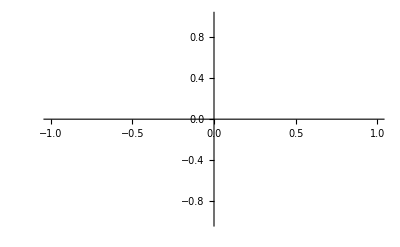

```mathematica
MPlusBand//ListPlot
```